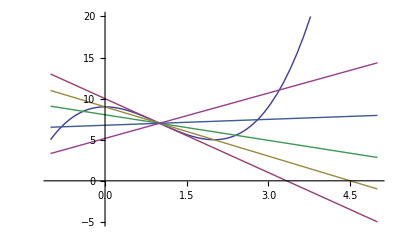

```mathematica
f[x_]=Expand[(x-1)^3-3(x-1)+7];
sec[a_,b_,x_]:=((f[a]-f[b])/(a-b))(x-a)+f[a];
Plot[{(x-1)^3-3(x-1)+7,f'[1](x-1)+f[1], sec[1,2,x],sec[1,2.4,x],sec[1,2.8,x],sec[1,3.2,x]},{x,-1,5},PlotRange->{-5,20}]
```

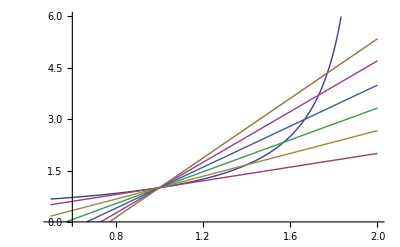

```mathematica
f[x_]=Expand[-1/(x-2)];
sec[a_,b_,x_]:=((f[a]-f[b])/(a-b))(x-a)+f[a];
Plot[{f[x],f'[1](x-1)+f[1], sec[1,1.4,x],sec[1,1.57,x],sec[1,1.666,x],sec[1,1.73,x],sec[1,1.77,x]},{x,.5,2},PlotRange->{0,6}]
```

```mathematica
Solve[f[x]==6.,x]
```

{{x→1.83333}}

```mathematica
Solve[f[1]+5*.6666==f[x],x]
```

{{x→1.76921}}

```mathematica
Expand[{sec[1,1.4,x],sec[1,1.57,x],sec[1,1.666,x],sec[1,1.73,x],sec[1,1.77,x]}]
```

{-0.666667+1.66667 x,-1.32558+2.32558 x,-1.99401+2.99401 x,-2.7037+3.7037 x,-3.34783+4.34783 x}

```mathematica
f[1.666]
```

2.99401

```mathematica
f[1.4]-f[1]
```

0.666667

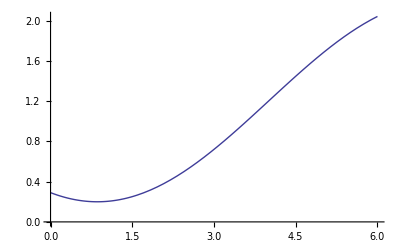

```mathematica
f[x_]=Sin[(x-4)/2]+1.2;
Plot[f[x],{x,0,6}]
```

```mathematica
Solve[f[x]==1,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→3.59728}}

```mathematica
f[1]
```

0.202505

```mathematica
f[5]
```

1.67943